```mathematica
sqHeight = 90;
sqStd = 120;
minHeight = 60;
maxHeight = 200;
viewingAngle = 50;
rk = 100;
SQ[z_] = PDF[NormalDistribution[sqHeight, sqStd], z] / PDF[NormalDistribution[sqHeight, sqStd], sqHeight];
R[z_, r_] = r*PDF[NormalDistribution[0, rk * r], z] / PDF[NormalDistribution[0, rk * r], minHeight];
Manipulate[Plot[{SQ[z] -  R[z, r]},{z,minHeight,maxHeight}], {r, 0.01, 1}]
```

```mathematica
SQPixel[z_] = minHeight ^ 2 / z ^ 2;
SQArea[z_] = (z ^2 - minHeight ^ 2) / (maxHeight ^ 2 -  minHeight^2);
Manipulate[Plot[{SQArea[z],SQPixel[z], R[z, r]}, {z, minHeight, maxHeight}],{r , 0.01, 1}]
```

```mathematica
rdata = Import["~/Documents/Projects/rover/sandbox/all.txt", "Table"];
ListPlot[
Transpose[rdata][[{1,2,3}]],
PlotLegends-> SwatchLegend[{"Area Coverage", "Sensor Quality", "Risk"}]]
```

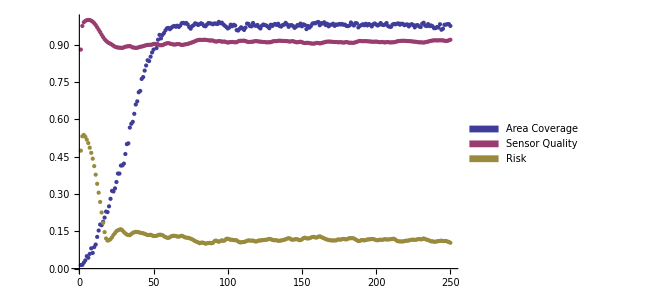

```mathematica
Al[z_, phi_, alpha_] = z * Tan[phi + alpha] - z * Tan[phi];
As[z_, phi_, alpha_] = z * Tan[alpha] / Cos[phi];
Epx[z_, phi_, alpha_, beta_, t_] =  z * Tan[phi - alpha]  + Al[z, phi, alpha] + Al[z, phi, alpha] * Cos[t];
Epy[z_, phi_, alpha_, beta_, t_] = As[z, phi, alpha] * Sin[t];
Manipulate[
ParametricPlot[
{Epx[z, phi, alpha,beta, t], Epy[z, phi, alpha,beta, t]}, {t, 0, 2 * Pi}
],{z, minHeight, maxHeight}, {phi, 0, Pi / 2 - alpha - 0.1}, {alpha, 0.01, Pi / 3}, {beta, 0, 2 * Pi}
]
```